```mathematica
a=Get[NotebookDirectory[]<>"pippo.txt"];
```

-Graphics3D-

-Graphics3D-

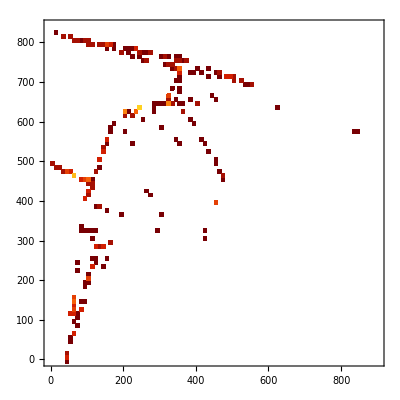

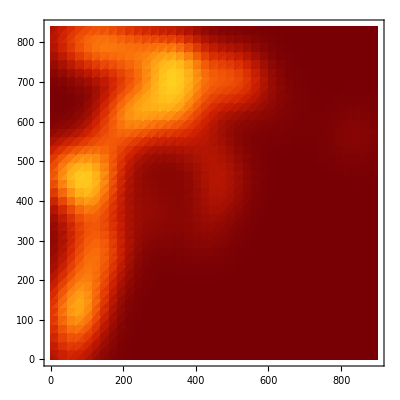

```mathematica
a1=Histogram3D[a,10,PlotRange->{{0,900},{0,840},{0,100}}]
a2=SmoothHistogram3D[a,PlotRange->{{0,900},{0,840},Automatic},PlotStyle->{Directive[ColorFunction->"SolarColors",Opacity[.5]]}]
a3= DensityHistogram[a,100,PlotRange->{{0,900},{0,840}}, ColorFunction->"SolarColors"]
a4= SmoothDensityHistogram[a,50,PlotRange->{{0,900},{0,840}}, ColorFunction->"SolarColors"]
```

```mathematica
img1=Import[NotebookDirectory[]<>"00-FASE0_a.jpg"]
```

-Graphics-

```mathematica
altezza=-0.5;
mappa=Graphics3D[{Texture[img1],Polygon[{{900,0,altezza},{0,0,altezza},{0,840,altezza},{900,840,altezza}},VertexTextureCoordinates->{{0,0},{-1,0},{-1,1},{0,1}}](*,
Lighting->"Neutral"*)}]
```

-Graphics3D-

```mathematica
Show[a2,mappa,PlotRange->{{0,900},{0,840},{-1,0.000001}}]
```

-Graphics3D-

```mathematica
Show[img1,a3]
```

-Graphics-

```mathematica
Show[a4,img1]
```

-Graphics-

```mathematica
img2=img1
```

-Graphics-

```mathematica
u=RemoveBackground[img2,{"Background",White}]
```

-Graphics-

```mathematica
Show[a4,u]
```

-Graphics-